## Matrix Element calculation

```mathematica
√((n!)/((n+nt-n)!))(ⅈ η 1)^(nt-n)LaguerreL[n,nt-n,(η 1)^2]Exp[-η^2/2]
```

```mathematica
nmax = 10;η = 0.2; τ = 1/(1.84 10^6)
```

5.43478×10^-7

```mathematica
LaguerreL[r,s,t] //Expand
```

LaguerreL[r,s,t]

```mathematica
Min[1,2]
```

1

```mathematica
Dr[n_,nt_]:= √((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η 1)^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η 1)^2]Exp[-η^2/2];
```

```mathematica
M[n_,nt_] :=NIntegrate[Sin[θ]/2 Abs[∑_(m=1)^nmax √((Min[n,m]!)/((Min[n,m]+Abs[m-n])!))(ⅈ η Cos[θ])^Abs[m-n] LaguerreL[Min[n,m],Abs[m-n],(η Cos[θ] 1)^2]Exp[-(η Cos[θ])^2/2] Dr[m,nt]]^2,{θ,0, Pi}]
```

```mathematica
Sum[Abs[Dr[n,3]]^2,{n,1,40}]
```

0.99999

```mathematica
M[1,2]
```

0.0890086+0. ⅈ

```mathematica
Dr[1,1]
```

0.940991+0. ⅈ

```mathematica
DrMat = Table[Dr[n,nt],{n,1,nmax},{nt,1,nmax}]
```

{{0.940991+0. ⅈ,0.+0.271697 ⅈ,-0.0473795+0. ⅈ,0.-0.0063386 ⅈ,0.000710109+0. ⅈ,0.+0.0000696697 ⅈ,-6.15018×10^-6+0. ⅈ,0.-4.97367×10^-7 ⅈ,3.73233×10^-8+0. ⅈ,0.+2.62399×10^-9 ⅈ},{0.+0.271697 ⅈ,0.902567+0. ⅈ,0.+0.326059 ⅈ,-0.0661083+0. ⅈ,0.-0.00992179 ⅈ,0.00122009+0. ⅈ,0.+0.00012947 ⅈ,-0.00001223+0. ⅈ,0.-1.0498×10^-6 ⅈ,8.30865×10^-8+0. ⅈ},{-0.0473795+0. ⅈ,0.+0.326059 ⅈ,0.864917+0. ⅈ,0.+0.368867 ⅈ,-0.0841997+0. ⅈ,0.-0.0138906 ⅈ,0.00184877+0. ⅈ,0.+0.000210012 ⅈ,-0.0000210618+0. ⅈ,0.-1.90706×10^-6 ⅈ},{0.-0.0063386 ⅈ,-0.0661083+0. ⅈ,0.+0.368867 ⅈ,0.82803+0. ⅈ,0.+0.403986 ⅈ,-0.101734+0. ⅈ,0.-0.0181907 ⅈ,0.00259356+0. ⅈ,0.+0.000312912 ⅈ,-0.0000331109+0. ⅈ},{0.000710109+0. ⅈ,0.-0.00992179 ⅈ,-0.0841997+0. ⅈ,0.+0.403986 ⅈ,0.791896+0. ⅈ,0.+0.433445 ⅈ,-0.118746+0. ⅈ,0.-0.0227777 ⅈ,0.00345163+0. ⅈ,0.+0.000439563 ⅈ},{0.+0.0000696697 ⅈ,0.00122009+0. ⅈ,0.-0.0138906 ⅈ,-0.101734+0. ⅈ,0.+0.433445 ⅈ,0.756506+0. ⅈ,0.+0.458479 ⅈ,-0.135257+0. ⅈ,0.-0.027615 ⅈ,0.00442015+0. ⅈ},{-6.15018×10^-6+0. ⅈ,0.+0.00012947 ⅈ,0.00184877+0. ⅈ,0.-0.0181907 ⅈ,-0.118746+0. ⅈ,0.+0.458479 ⅈ,0.721848+0. ⅈ,0.+0.47991 ⅈ,-0.151279+0. ⅈ,0.-0.0326721 ⅈ},{0.-4.97367×10^-7 ⅈ,-0.00001223+0. ⅈ,0.+0.000210012 ⅈ,0.00259356+0. ⅈ,0.-0.0227777 ⅈ,-0.135257+0. ⅈ,0.+0.47991 ⅈ,0.687913+0. ⅈ,0.+0.498324 ⅈ,-0.166825+0. ⅈ},{3.73233×10^-8+0. ⅈ,0.-1.0498×10^-6 ⅈ,-0.0000210618+0. ⅈ,0.+0.000312912 ⅈ,0.00345163+0. ⅈ,0.-0.027615 ⅈ,-0.151279+0. ⅈ,0.+0.498324 ⅈ,0.654692+0. ⅈ,0.+0.514158 ⅈ},{0.+2.62399×10^-9 ⅈ,8.30865×10^-8+0. ⅈ,0.-1.90706×10^-6 ⅈ,-0.0000331109+0. ⅈ,0.+0.000439563 ⅈ,0.00442015+0. ⅈ,0.-0.0326721 ⅈ,-0.166825+0. ⅈ,0.+0.514158 ⅈ,0.622173+0. ⅈ}}

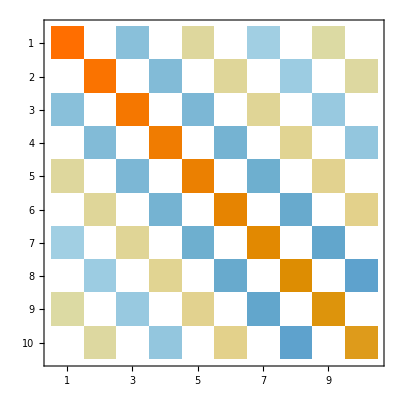

```mathematica
MatrixPlot[DrMat]
```

```mathematica
M[1,1]
```

85.1019

```mathematica
Mat = Table[M[n,nt],{n,1,nmax},{nt,1,nmax}]
```

{{0.854275,0.0890086+0. ⅈ,0.00638561,0.000324538+0. ⅈ,0.0000126444,3.98087×10^-7+0. ⅈ,1.04998×10^-8,2.3811×10^-10+0. ⅈ,4.73402×10^-12,8.37794×10^-14+0. ⅈ},{0.0890363+0. ⅈ,0.776546,0.120051+0. ⅈ,0.0117555,0.000759721+0. ⅈ,0.0000359313,1.33045×10^-6+0. ⅈ,4.03424×10^-8,1.0339×10^-9+0. ⅈ,2.29267×10^-11},{0.00637046,0.120059+0. ⅈ,0.708382,0.145467+0. ⅈ,0.0181374,0.00142649+0. ⅈ,0.0000795059,3.38945×10^-6+0. ⅈ,1.16273×10^-7,3.32717×10^-9+0. ⅈ},{0.000324102+0. ⅈ,0.0117557,0.145467+0. ⅈ,0.649504,0.165266+0. ⅈ,0.0251786,0.00234313+0. ⅈ,0.00015077,7.28449×10^-6+0. ⅈ,2.79538×10^-7},{0.0000126358,0.000759727+0. ⅈ,0.0181374,0.165266+0. ⅈ,0.599102,0.180316+0. ⅈ,0.0326158,0.00351821+0. ⅈ,0.000257234,0.0000139493+0. ⅈ},{3.97959×10^-7+0. ⅈ,0.0000359314,0.00142649+0. ⅈ,0.0251786,0.180316+0. ⅈ,0.556067,0.191363+0. ⅈ,0.0402312,0.00494878+0. ⅈ,0.00040875},{1.04982×10^-8,1.33045×10^-6+0. ⅈ,0.0000795059,0.00234313+0. ⅈ,0.0326158,0.191362+0. ⅈ,0.519405,0.19909+0. ⅈ,0.0477632,0.0067284+0. ⅈ},{2.38093×10^-10+0. ⅈ,4.03424×10^-8,3.38946×10^-6+0. ⅈ,0.00015077,0.00351823+0. ⅈ,0.0402318,0.199086+0. ⅈ,0.487956,0.203254+0. ⅈ,0.0572303},{4.73383×10^-12+0. ⅈ,1.03389×10^-9+0. ⅈ,1.16269×10^-7+0. ⅈ,7.28397×10^-6+0. ⅈ,0.000257189+0. ⅈ,0.00494661+0. ⅈ,0.0477114+0. ⅈ,0.202304+0. ⅈ,0.448756+0. ⅈ,0.231549+0. ⅈ},{8.37906×10^-14+0. ⅈ,2.29341×10^-11+0. ⅈ,3.32953×10^-9+0. ⅈ,2.79974×10^-7+0. ⅈ,0.0000139973+0. ⅈ,0.000411829+0. ⅈ,0.00683498+0. ⅈ,0.0589273+0. ⅈ,0.226939+0. ⅈ,0.334469+0. ⅈ}}

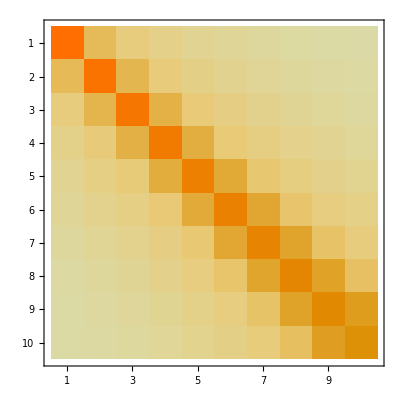

```mathematica
MatrixPlot[Mat]
```

```mathematica
Master equation for Raman- 3 level system
```

```mathematica
Clear[α, η]
```

```mathematica
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ωR}, {0, ωR, -2 δ2}})
```

{{-hbar δ1,(hbar Ωn)/2,0},{(hbar Ωn)/2,0,(hbar ωR)/2},{0,(hbar ωR)/2,-hbar δ2}}

```mathematica
Γ1 = α η^2 n Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
```

```mathematica
Γo = Γ - Γ1 - Γ2;
```

```mathematica
L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}})
```

{{n α Γ η^2 ρ33[t],0,-1/2 Γ ρ13[t]},{0,(1-α) Γ (1-(-1+2 n) η^2) ρ33[t],-1/2 Γ ρ23[t]},{-1/2 Γ ρ31[t],-1/2 Γ ρ32[t],-Γ ρ33[t]}}

```mathematica
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}})
```

```mathematica
dρdt = -ⅈ/hbar(H. ρe[t]- ρe[t]. H)+ L//FullSimplify
```

{{1/2 ⅈ Ωn (ρ12[t]-ρ21[t])+n α Γ η^2 ρ33[t],1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ12[t]+ωR ρ13[t]-Ωn ρ22[t]),1/2 ⅈ (ωR ρ12[t]+(ⅈ Γ+2 δ1-2 δ2) ρ13[t]-Ωn ρ23[t])},{-1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ21[t]-Ωn ρ22[t]+ωR ρ31[t]),-1/2 ⅈ (Ωn ρ12[t]-Ωn ρ21[t]+ωR (-ρ23[t]+ρ32[t]))+(-1+α) Γ (-1+(-1+2 n) η^2) ρ33[t],-1/2 ⅈ (Ωn ρ13[t]-ωR ρ22[t]-ⅈ Γ ρ23[t]+2 δ2 ρ23[t]+ωR ρ33[t])},{-1/2 ⅈ (ωR ρ21[t]+(-ⅈ Γ+2 δ1-2 δ2) ρ31[t]-Ωn ρ32[t]),-1/2 ⅈ (ωR ρ22[t]-Ωn ρ31[t]-ⅈ Γ ρ32[t]-2 δ2 ρ32[t]-ωR ρ33[t]),-1/2 ⅈ ωR (ρ23[t]-ρ32[t])-Γ ρ33[t]}}

```mathematica
ρef = Flatten[ρe'[t]]
```

{ρ11'[t],ρ12'[t],ρ13'[t],ρ21'[t],ρ22'[t],ρ23'[t],ρ31'[t],ρ32'[t],ρ33'[t]}

```mathematica
ρef2 = Flatten[ρe[t]]
```

{ρ11[t],ρ12[t],ρ13[t],ρ21[t],ρ22[t],ρ23[t],ρ31[t],ρ32[t],ρ33[t]}

```mathematica
dρdtf= Flatten[dρdt]
```

{1/2 ⅈ Ωn (ρ12[t]-ρ21[t])+n α Γ η^2 ρ33[t],1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ12[t]+ωR ρ13[t]-Ωn ρ22[t]),1/2 ⅈ (ωR ρ12[t]+(ⅈ Γ+2 δ1-2 δ2) ρ13[t]-Ωn ρ23[t]),-1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ21[t]-Ωn ρ22[t]+ωR ρ31[t]),-1/2 ⅈ (Ωn ρ12[t]-Ωn ρ21[t]+ωR (-ρ23[t]+ρ32[t]))+(-1+α) Γ (-1+(-1+2 n) η^2) ρ33[t],-1/2 ⅈ (Ωn ρ13[t]-ωR ρ22[t]-ⅈ Γ ρ23[t]+2 δ2 ρ23[t]+ωR ρ33[t]),-1/2 ⅈ (ωR ρ21[t]+(-ⅈ Γ+2 δ1-2 δ2) ρ31[t]-Ωn ρ32[t]),-1/2 ⅈ (ωR ρ22[t]-Ωn ρ31[t]-ⅈ Γ ρ32[t]-2 δ2 ρ32[t]-ωR ρ33[t]),-1/2 ⅈ ωR (ρ23[t]-ρ32[t])-Γ ρ33[t]}

```mathematica
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]]
```

{ρ11'[t]==1/2 ⅈ Ωn (ρ12[t]-ρ21[t])+n α Γ η^2 ρ33[t],ρ12'[t]==1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ12[t]+ωR ρ13[t]-Ωn ρ22[t]),ρ13'[t]==1/2 ⅈ (ωR ρ12[t]+(ⅈ Γ+2 δ1-2 δ2) ρ13[t]-Ωn ρ23[t]),ρ21'[t]==-1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ21[t]-Ωn ρ22[t]+ωR ρ31[t]),ρ22'[t]==1/2 (-ⅈ (Ωn ρ12[t]-Ωn ρ21[t]+ωR (-ρ23[t]+ρ32[t]))+(-1+α) Γ (-1+(-1+2 n) η^2) ρ33[t]),ρ23'[t]==-1/2 ⅈ (Ωn ρ13[t]-ωR ρ22[t]-ⅈ Γ ρ23[t]+2 δ2 ρ23[t]+ωR ρ33[t]),ρ31'[t]==-1/2 ⅈ (ωR ρ21[t]+(-ⅈ Γ+2 δ1-2 δ2) ρ31[t]-Ωn ρ32[t]),ρ32'[t]==-1/2 ⅈ (ωR ρ22[t]-Ωn ρ31[t]-ⅈ Γ ρ32[t]-2 δ2 ρ32[t]-ωR ρ33[t]),ρ33'[t]==-1/2 ⅈ ωR (ρ23[t]-ρ32[t])-Γ ρ33[t]}

```mathematica
sol=DSolve[system,ρef2,t]
```

```mathematica
system = Table[0 == Part[dρdtf,j],{j,1,9,1}]
```

{0==1/2 ⅈ Ωn (ρ12[t]-ρ21[t])+n α Γ η^2 ρ33[t],0==1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ12[t]+ωR ρ13[t]-Ωn ρ22[t]),0==1/2 ⅈ (ωR ρ12[t]+(ⅈ Γ+2 δ1-2 δ2) ρ13[t]-Ωn ρ23[t]),0==-1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ21[t]-Ωn ρ22[t]+ωR ρ31[t]),0==-1/2 ⅈ (Ωn ρ12[t]-Ωn ρ21[t]+ωR (-ρ23[t]+ρ32[t]))+(-1+α) Γ (-1+(-1+2 n) η^2) ρ33[t],0==-1/2 ⅈ (Ωn ρ13[t]-ωR ρ22[t]-ⅈ Γ ρ23[t]+2 δ2 ρ23[t]+ωR ρ33[t]),0==-1/2 ⅈ (ωR ρ21[t]+(-ⅈ Γ+2 δ1-2 δ2) ρ31[t]-Ωn ρ32[t]),0==-1/2 ⅈ (ωR ρ22[t]-Ωn ρ31[t]-ⅈ Γ ρ32[t]-2 δ2 ρ32[t]-ωR ρ33[t]),0==-1/2 ⅈ ωR (ρ23[t]-ρ32[t])-Γ ρ33[t]}

```mathematica
system
```

```mathematica
Solve[system, ρef2]
```

{{ρ11[t]→0,ρ12[t]→0,ρ13[t]→0,ρ21[t]→0,ρ22[t]→0,ρ23[t]→0,ρ31[t]→0,ρ32[t]→0,ρ33[t]→0}}

```mathematica
no steady state solution as system is not closed, one can look at solutions with constant decay rates instead
```